# Collusion of policy-pairs

Converts a number n to a list of binary digits. Padded so that the list has length l

```mathematica
toBin[n_,l_]:= Join[ConstantArray[0,l-Length[IntegerDigits[n,2]]],IntegerDigits[n,2]];
```

Checks if a policy-pair is colluding

{{(1-e)^2,(1-e) e,(1-e) e,e^2},{(1-e) e,(1-e)^2,e^2,(1-e) e},{(1-e)^2,(1-e) e,(1-e) e,e^2},{e^2,(1-e) e,(1-e) e,(1-e)^2}}

DiscreteMarkovProcess[{1/4,1/4,1/4,1/4},{{(1-e)^2,(1-e) e,(1-e) e,e^2},{(1-e) e,(1-e)^2,e^2,(1-e) e},{(1-e)^2,(1-e) e,(1-e) e,e^2},{e^2,(1-e) e,(1-e) e,(1-e)^2}}]

{(3-6 e+4 e^2)/(4-2 (-1+e)-6 e+4 e^2-4 (-e+e^2)),-(2 (-1+e))/(4-2 (-1+e)-6 e+4 e^2-4 (-e+e^2)),-(4 (-e+e^2))/(4-2 (-1+e)-6 e+4 e^2-4 (-e+e^2)),1/(4-2 (-1+e)-6 e+4 e^2-4 (-e+e^2))}

{3+8 e^2>12 e,1+2 (-2+e) e>0,False,1+4 e^2>6 e}

{1+4 e^2,6 e}

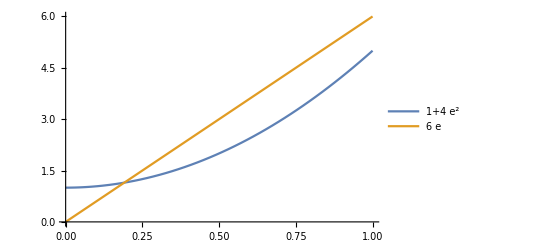

0 | {0,0,0,0,0,0,0,0} | {1,0,0,0} | {1} | {same}
1 | {0,0,0,0,0,0,0,1} | {1,0,0,0} | {1} | {}
2 | {0,0,0,0,0,0,1,0} | {2/3,1/3,0,0} | {1,2} | {}
3 | {0,0,0,0,0,0,1,1} | {1/2,1/2,0,0} | {1,2} | {}
4 | {0,0,0,0,0,1,0,0} | {1,0,0,0} | {1} | {}
5 | {0,0,0,0,0,1,0,1} | {1,0,0,0} | {1} | {}
6 | {0,0,0,0,0,1,1,0} | {1/2,1/2,0,0} | {1,2} | {compmid}
7 | {0,0,0,0,0,1,1,1} | {1/3,2/3,0,0} | {1,2} | {}
8 | {0,0,0,0,1,0,0,0} | {1/2,1/2,0,0} | {1,2} | {}
9 | {0,0,0,0,1,0,0,1} | {1/2,1/2,0,0} | {1,2} | {compside}
10 | {0,0,0,0,1,0,1,0} | {0,1,0,0} | {2} | {}
11 | {0,0,0,0,1,0,1,1} | {0,1,0,0} | {2} | {}
12 | {0,0,0,0,1,1,0,0} | {1/2,1/2,0,0} | {1,2} | {}
13 | {0,0,0,0,1,1,0,1} | {1/2,1/2,0,0} | {1,2} | {}
14 | {0,0,0,0,1,1,1,0} | {0,1,0,0} | {2} | {}
15 | {0,0,0,0,1,1,1,1} | {0,1,0,0} | {2} | {comp}
16 | {0,0,0,1,0,0,0,0} | {1,0,0,0} | {1} | {}
17 | {0,0,0,1,0,0,0,1} | {1,0,0,0} | {1} | {same}
18 | {0,0,0,1,0,0,1,0} | {2/3,1/3,0,0} | {1,2} | {}
19 | {0,0,0,1,0,0,1,1} | {1/2,1/3,0,1/6} | {1,2,4} | {}
20 | {0,0,0,1,0,1,0,0} | {1,0,0,0} | {1} | {}
21 | {0,0,0,1,0,1,0,1} | {1,0,0,0} | {1} | {}
22 | {0,0,0,1,0,1,1,0} | {1/3,2/3,0,0} | {1,2} | {}
23 | {0,0,0,1,0,1,1,1} | {1/4,1/2,0,1/4} | {1,2,4} | {compmid}
24 | {0,0,0,1,1,0,0,0} | {1/2,1/2,0,0} | {1,2} | {compside}
25 | {0,0,0,1,1,0,0,1} | {2/5,2/5,0,1/5} | {1,2,4} | {}
26 | {0,0,0,1,1,0,1,0} | {0,1,0,0} | {2} | {}
27 | {0,0,0,1,1,0,1,1} | {0,2/3,0,1/3} | {2,4} | {}
28 | {0,0,0,1,1,1,0,0} | {1/2,1/2,0,0} | {1,2} | {}
29 | {0,0,0,1,1,1,0,1} | {2/5,2/5,0,1/5} | {1,2,4} | {}
30 | {0,0,0,1,1,1,1,0} | {0,1,0,0} | {2} | {comp}
31 | {0,0,0,1,1,1,1,1} | {0,2/3,0,1/3} | {2,4} | {}
32 | {0,0,1,0,0,0,0,0} | {2/3,0,1/3,0} | {1,3} | {}
33 | {0,0,1,0,0,0,0,1} | {2/3,0,1/3,0} | {1,3} | {}
34 | {0,0,1,0,0,0,1,0} | {1/2,1/4,1/4,0} | {1,2,3} | {same}
35 | {0,0,1,0,0,0,1,1} | {1/3,1/2,1/6,0} | {1,2,3} | {}
36 | {0,0,1,0,0,1,0,0} | {1,0,0,0} | {1} | {compmid}
37 | {0,0,1,0,0,1,0,1} | {1,0,0,0} | {1} | {}
38 | {0,0,1,0,0,1,1,0} | {2/3,1/3,0,0} | {1,2} | {}
39 | {0,0,1,0,0,1,1,1} | {1/3,2/3,0,0} | {1,2} | {}
40 | {0,0,1,0,1,0,0,0} | {2/5,2/5,1/5,0} | {1,2,3} | {}
41 | {0,0,1,0,1,0,0,1} | {2/5,2/5,1/5,0} | {1,2,3} | {}
42 | {0,0,1,0,1,0,1,0} | {0,1,0,0} | {2} | {}
43 | {0,0,1,0,1,0,1,1} | {0,1,0,0} | {2} | {compside}
44 | {0,0,1,0,1,1,0,0} | {1/2,1/2,0,0} | {1,2} | {}
45 | {0,0,1,0,1,1,0,1} | {1/2,1/2,0,0} | {1,2} | {comp}
46 | {0,0,1,0,1,1,1,0} | {0,1,0,0} | {2} | {}
47 | {0,0,1,0,1,1,1,1} | {0,1,0,0} | {2} | {}
48 | {0,0,1,1,0,0,0,0} | {1/2,0,1/2,0} | {1,3} | {}
49 | {0,0,1,1,0,0,0,1} | {1/2,0,1/3,1/6} | {1,3,4} | {}
50 | {0,0,1,1,0,0,1,0} | {1/3,1/6,1/2,0} | {1,2,3} | {}
51 | {0,0,1,1,0,0,1,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {same}
52 | {0,0,1,1,0,1,0,0} | {1/2,0,1/4,1/4} | {1,3,4} | {}
53 | {0,0,1,1,0,1,0,1} | {1/2,0,0,1/2} | {1,4} | {compmid}
54 | {0,0,1,1,0,1,1,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
55 | {0,0,1,1,0,1,1,1} | {1/6,1/3,0,1/2} | {1,2,4} | {}
56 | {0,0,1,1,1,0,0,0} | {1/4,1/4,1/2,0} | {1,2,3} | {}
57 | {0,0,1,1,1,0,0,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
58 | {0,0,1,1,1,0,1,0} | {0,1/2,1/2,0} | {2,3} | {compside}
59 | {0,0,1,1,1,0,1,1} | {0,1/2,1/6,1/3} | {2,3,4} | {}
60 | {0,0,1,1,1,1,0,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {comp}
61 | {0,0,1,1,1,1,0,1} | {1/4,1/4,0,1/2} | {1,2,4} | {}
62 | {0,0,1,1,1,1,1,0} | {0,1/2,1/4,1/4} | {2,3,4} | {}
63 | {0,0,1,1,1,1,1,1} | {0,1/2,0,1/2} | {2,4} | {}
64 | {0,1,0,0,0,0,0,0} | {1,0,0,0} | {1} | {}
65 | {0,1,0,0,0,0,0,1} | {1,0,0,0} | {1} | {}
66 | {0,1,0,0,0,0,1,0} | {1,0,0,0} | {1} | {compmid}
67 | {0,1,0,0,0,0,1,1} | {1/2,1/4,0,1/4} | {1,2,4} | {}
68 | {0,1,0,0,0,1,0,0} | {1/2,1/4,1/4,0} | {1,2,3} | {same}
69 | {0,1,0,0,0,1,0,1} | {1/3,1/3,1/3,0} | {1,2,3} | {}
70 | {0,1,0,0,0,1,1,0} | {1,0,0,0} | {1} | {}
71 | {0,1,0,0,0,1,1,1} | {1/5,2/5,0,2/5} | {1,2,4} | {}
72 | {0,1,0,0,1,0,0,0} | {1/3,1/3,1/3,0} | {1,2,3} | {}
73 | {0,1,0,0,1,0,0,1} | {1/3,1/3,1/3,0} | {1,2,3} | {}
74 | {0,1,0,0,1,0,1,0} | {1/3,1/3,0,1/3} | {1,2,4} | {}
75 | {0,1,0,0,1,0,1,1} | {0,1/2,0,1/2} | {2,4} | {comp}
76 | {0,1,0,0,1,1,0,0} | {0,1/2,1/2,0} | {2,3} | {}
77 | {0,1,0,0,1,1,0,1} | {0,1/2,1/2,0} | {2,3} | {compside}
78 | {0,1,0,0,1,1,1,0} | {1/3,1/3,0,1/3} | {1,2,4} | {}
79 | {0,1,0,0,1,1,1,1} | {0,1/2,0,1/2} | {2,4} | {}
80 | {0,1,0,1,0,0,0,0} | {1,0,0,0} | {1} | {}
81 | {0,1,0,1,0,0,0,1} | {1,0,0,0} | {1} | {}
82 | {0,1,0,1,0,0,1,0} | {1,0,0,0} | {1} | {}
83 | {0,1,0,1,0,0,1,1} | {1/2,0,0,1/2} | {1,4} | {compmid}
84 | {0,1,0,1,0,1,0,0} | {1/3,1/3,1/3,0} | {1,2,3} | {}
85 | {0,1,0,1,0,1,0,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {same}
86 | {0,1,0,1,0,1,1,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
87 | {0,1,0,1,0,1,1,1} | {0,0,0,1} | {4} | {}
88 | {0,1,0,1,1,0,0,0} | {1/3,1/3,1/3,0} | {1,2,3} | {}
89 | {0,1,0,1,1,0,0,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
90 | {0,1,0,1,1,0,1,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {comp}
91 | {0,1,0,1,1,0,1,1} | {0,0,0,1} | {4} | {}
92 | {0,1,0,1,1,1,0,0} | {0,1/2,1/2,0} | {2,3} | {compside}
93 | {0,1,0,1,1,1,0,1} | {0,1/3,1/3,1/3} | {2,3,4} | {}
94 | {0,1,0,1,1,1,1,0} | {0,1/3,1/3,1/3} | {2,3,4} | {}
95 | {0,1,0,1,1,1,1,1} | {0,0,0,1} | {4} | {}
96 | {0,1,1,0,0,0,0,0} | {1/2,0,1/2,0} | {1,3} | {compmid}
97 | {0,1,1,0,0,0,0,1} | {1/3,0,2/3,0} | {1,3} | {}
98 | {0,1,1,0,0,0,1,0} | {2/3,0,1/3,0} | {1,3} | {}
99 | {0,1,1,0,0,0,1,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
100 | {0,1,1,0,0,1,0,0} | {1,0,0,0} | {1} | {}
101 | {0,1,1,0,0,1,0,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
102 | {0,1,1,0,0,1,1,0} | {1,0,0,0} | {1} | {same}
103 | {0,1,1,0,0,1,1,1} | {1/5,2/5,0,2/5} | {1,2,4} | {}
104 | {0,1,1,0,1,0,0,0} | {0,0,1,0} | {3} | {}
105 | {0,1,1,0,1,0,0,1} | {0,0,1,0} | {3} | {comp}
106 | {0,1,1,0,1,0,1,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
107 | {0,1,1,0,1,0,1,1} | {0,2/5,1/5,2/5} | {2,3,4} | {}
108 | {0,1,1,0,1,1,0,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
109 | {0,1,1,0,1,1,0,1} | {0,1/3,1/3,1/3} | {2,3,4} | {}
110 | {0,1,1,0,1,1,1,0} | {1/3,1/3,0,1/3} | {1,2,4} | {}
111 | {0,1,1,0,1,1,1,1} | {0,1/2,0,1/2} | {2,4} | {compside}
112 | {0,1,1,1,0,0,0,0} | {1/3,0,2/3,0} | {1,3} | {}
113 | {0,1,1,1,0,0,0,1} | {1/4,0,1/2,1/4} | {1,3,4} | {compmid}
114 | {0,1,1,1,0,0,1,0} | {1/3,0,2/3,0} | {1,3} | {}
115 | {0,1,1,1,0,0,1,1} | {1/6,0,1/3,1/2} | {1,3,4} | {}
116 | {0,1,1,1,0,1,0,0} | {1/5,0,2/5,2/5} | {1,3,4} | {}
117 | {0,1,1,1,0,1,0,1} | {0,0,0,1} | {4} | {}
118 | {0,1,1,1,0,1,1,0} | {1/5,0,2/5,2/5} | {1,3,4} | {}
119 | {0,1,1,1,0,1,1,1} | {0,0,0,1} | {4} | {same}
120 | {0,1,1,1,1,0,0,0} | {0,0,1,0} | {3} | {comp}
121 | {0,1,1,1,1,0,0,1} | {0,0,2/3,1/3} | {3,4} | {}
122 | {0,1,1,1,1,0,1,0} | {0,0,1,0} | {3} | {}
123 | {0,1,1,1,1,0,1,1} | {0,0,1/3,2/3} | {3,4} | {}
124 | {0,1,1,1,1,1,0,0} | {0,0,1/2,1/2} | {3,4} | {}
125 | {0,1,1,1,1,1,0,1} | {0,0,0,1} | {4} | {}
126 | {0,1,1,1,1,1,1,0} | {0,0,1/2,1/2} | {3,4} | {compside}
127 | {0,1,1,1,1,1,1,1} | {0,0,0,1} | {4} | {}
128 | {1,0,0,0,0,0,0,0} | {1/2,0,1/2,0} | {1,3} | {}
129 | {1,0,0,0,0,0,0,1} | {1/2,0,1/2,0} | {1,3} | {compside}
130 | {1,0,0,0,0,0,1,0} | {2/5,1/5,2/5,0} | {1,2,3} | {}
131 | {1,0,0,0,0,0,1,1} | {1/4,1/2,1/4,0} | {1,2,3} | {}
132 | {1,0,0,0,0,1,0,0} | {1/3,1/3,1/3,0} | {1,2,3} | {}
133 | {1,0,0,0,0,1,0,1} | {1/3,1/3,1/3,0} | {1,2,3} | {}
134 | {1,0,0,0,0,1,1,0} | {0,1,0,0} | {2} | {}
135 | {1,0,0,0,0,1,1,1} | {0,1,0,0} | {2} | {comp}
136 | {1,0,0,0,1,0,0,0} | {1/2,0,0,1/2} | {1,4} | {same}
137 | {1,0,0,0,1,0,0,1} | {1/3,1/3,0,1/3} | {1,2,4} | {}
138 | {1,0,0,0,1,0,1,0} | {1/3,1/3,0,1/3} | {1,2,4} | {}
139 | {1,0,0,0,1,0,1,1} | {0,1,0,0} | {2} | {}
140 | {1,0,0,0,1,1,0,0} | {1/2,0,0,1/2} | {1,4} | {}
141 | {1,0,0,0,1,1,0,1} | {1/3,1/3,0,1/3} | {1,2,4} | {}
142 | {1,0,0,0,1,1,1,0} | {1/4,1/2,0,1/4} | {1,2,4} | {compmid}
143 | {1,0,0,0,1,1,1,1} | {0,1,0,0} | {2} | {}
144 | {1,0,0,1,0,0,0,0} | {1/2,0,1/2,0} | {1,3} | {compside}
145 | {1,0,0,1,0,0,0,1} | {2/5,0,2/5,1/5} | {1,3,4} | {}
146 | {1,0,0,1,0,0,1,0} | {2/5,1/5,2/5,0} | {1,2,3} | {}
147 | {1,0,0,1,0,0,1,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
148 | {1,0,0,1,0,1,0,0} | {1/3,1/3,1/3,0} | {1,2,3} | {}
149 | {1,0,0,1,0,1,0,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
150 | {1,0,0,1,0,1,1,0} | {0,1,0,0} | {2} | {comp}
151 | {1,0,0,1,0,1,1,1} | {0,2/3,0,1/3} | {2,4} | {}
152 | {1,0,0,1,1,0,0,0} | {1/3,0,1/3,1/3} | {1,3,4} | {}
153 | {1,0,0,1,1,0,0,1} | {0,0,0,1} | {4} | {same}
154 | {1,0,0,1,1,0,1,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
155 | {1,0,0,1,1,0,1,1} | {0,1/3,0,2/3} | {2,4} | {}
156 | {1,0,0,1,1,1,0,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
157 | {1,0,0,1,1,1,0,1} | {0,0,0,1} | {4} | {}
158 | {1,0,0,1,1,1,1,0} | {0,1,0,0} | {2} | {}
159 | {1,0,0,1,1,1,1,1} | {0,1/2,0,1/2} | {2,4} | {compmid}
160 | {1,0,1,0,0,0,0,0} | {0,0,1,0} | {3} | {}
161 | {1,0,1,0,0,0,0,1} | {0,0,1,0} | {3} | {}
162 | {1,0,1,0,0,0,1,0} | {0,0,1,0} | {3} | {}
163 | {1,0,1,0,0,0,1,1} | {0,1/2,1/2,0} | {2,3} | {compside}
164 | {1,0,1,0,0,1,0,0} | {1/3,0,1/3,1/3} | {1,3,4} | {}
165 | {1,0,1,0,0,1,0,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {comp}
166 | {1,0,1,0,0,1,1,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
167 | {1,0,1,0,0,1,1,1} | {0,1,0,0} | {2} | {}
168 | {1,0,1,0,1,0,0,0} | {1/3,0,1/3,1/3} | {1,3,4} | {}
169 | {1,0,1,0,1,0,0,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
170 | {1,0,1,0,1,0,1,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {same}
171 | {1,0,1,0,1,0,1,1} | {0,1,0,0} | {2} | {}
172 | {1,0,1,0,1,1,0,0} | {1/2,0,0,1/2} | {1,4} | {compmid}
173 | {1,0,1,0,1,1,0,1} | {1/3,1/3,0,1/3} | {1,2,4} | {}
174 | {1,0,1,0,1,1,1,0} | {1/3,1/3,0,1/3} | {1,2,4} | {}
175 | {1,0,1,0,1,1,1,1} | {0,1,0,0} | {2} | {}
176 | {1,0,1,1,0,0,0,0} | {0,0,1,0} | {3} | {}
177 | {1,0,1,1,0,0,0,1} | {0,0,2/3,1/3} | {3,4} | {}
178 | {1,0,1,1,0,0,1,0} | {0,0,1,0} | {3} | {compside}
179 | {1,0,1,1,0,0,1,1} | {0,1/6,1/2,1/3} | {2,3,4} | {}
180 | {1,0,1,1,0,1,0,0} | {0,0,1/2,1/2} | {3,4} | {comp}
181 | {1,0,1,1,0,1,0,1} | {0,0,0,1} | {4} | {}
182 | {1,0,1,1,0,1,1,0} | {0,1/5,2/5,2/5} | {2,3,4} | {}
183 | {1,0,1,1,0,1,1,1} | {0,1/3,0,2/3} | {2,4} | {}
184 | {1,0,1,1,1,0,0,0} | {0,0,1,0} | {3} | {}
185 | {1,0,1,1,1,0,0,1} | {0,0,1/3,2/3} | {3,4} | {}
186 | {1,0,1,1,1,0,1,0} | {0,0,1,0} | {3} | {}
187 | {1,0,1,1,1,0,1,1} | {0,1/4,1/4,1/2} | {2,3,4} | {same}
188 | {1,0,1,1,1,1,0,0} | {0,0,1/2,1/2} | {3,4} | {}
189 | {1,0,1,1,1,1,0,1} | {0,0,0,1} | {4} | {compmid}
190 | {1,0,1,1,1,1,1,0} | {0,1/5,2/5,2/5} | {2,3,4} | {}
191 | {1,0,1,1,1,1,1,1} | {0,1/3,0,2/3} | {2,4} | {}
192 | {1,1,0,0,0,0,0,0} | {1/2,0,1/2,0} | {1,3} | {}
193 | {1,1,0,0,0,0,0,1} | {1/2,0,1/2,0} | {1,3} | {}
194 | {1,1,0,0,0,0,1,0} | {1/2,0,1/2,0} | {1,3} | {}
195 | {1,1,0,0,0,0,1,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {comp}
196 | {1,1,0,0,0,1,0,0} | {0,1/2,1/2,0} | {2,3} | {}
197 | {1,1,0,0,0,1,0,1} | {0,1/2,1/2,0} | {2,3} | {compside}
198 | {1,1,0,0,0,1,1,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
199 | {1,1,0,0,0,1,1,1} | {0,1/2,0,1/2} | {2,4} | {}
200 | {1,1,0,0,1,0,0,0} | {1/2,0,0,1/2} | {1,4} | {}
201 | {1,1,0,0,1,0,0,1} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {}
202 | {1,1,0,0,1,0,1,0} | {1/2,0,0,1/2} | {1,4} | {compmid}
203 | {1,1,0,0,1,0,1,1} | {0,1/2,0,1/2} | {2,4} | {}
204 | {1,1,0,0,1,1,0,0} | {1/4,1/4,1/4,1/4} | {1,2,3,4} | {same}
205 | {1,1,0,0,1,1,0,1} | {0,1/2,1/2,0} | {2,3} | {}
206 | {1,1,0,0,1,1,1,0} | {1/2,0,0,1/2} | {1,4} | {}
207 | {1,1,0,0,1,1,1,1} | {0,1/2,0,1/2} | {2,4} | {}
208 | {1,1,0,1,0,0,0,0} | {1/2,0,1/2,0} | {1,3} | {}
209 | {1,1,0,1,0,0,0,1} | {2/5,0,2/5,1/5} | {1,3,4} | {}
210 | {1,1,0,1,0,0,1,0} | {1/2,0,1/2,0} | {1,3} | {comp}
211 | {1,1,0,1,0,0,1,1} | {1/4,0,1/4,1/2} | {1,3,4} | {}
212 | {1,1,0,1,0,1,0,0} | {0,1/2,1/2,0} | {2,3} | {compside}
213 | {1,1,0,1,0,1,0,1} | {0,1/3,1/3,1/3} | {2,3,4} | {}
214 | {1,1,0,1,0,1,1,0} | {0,1/3,1/3,1/3} | {2,3,4} | {}
215 | {1,1,0,1,0,1,1,1} | {0,0,0,1} | {4} | {}
216 | {1,1,0,1,1,0,0,0} | {1/3,0,1/3,1/3} | {1,3,4} | {}
217 | {1,1,0,1,1,0,0,1} | {0,0,0,1} | {4} | {}
218 | {1,1,0,1,1,0,1,0} | {1/3,0,1/3,1/3} | {1,3,4} | {}
219 | {1,1,0,1,1,0,1,1} | {0,0,0,1} | {4} | {compmid}
220 | {1,1,0,1,1,1,0,0} | {0,1/2,1/2,0} | {2,3} | {}
221 | {1,1,0,1,1,1,0,1} | {0,1/4,1/4,1/2} | {2,3,4} | {same}
222 | {1,1,0,1,1,1,1,0} | {0,1/3,1/3,1/3} | {2,3,4} | {}
223 | {1,1,0,1,1,1,1,1} | {0,0,0,1} | {4} | {}
224 | {1,1,1,0,0,0,0,0} | {0,0,1,0} | {3} | {}
225 | {1,1,1,0,0,0,0,1} | {0,0,1,0} | {3} | {comp}
226 | {1,1,1,0,0,0,1,0} | {0,0,1,0} | {3} | {}
227 | {1,1,1,0,0,0,1,1} | {0,1/4,1/2,1/4} | {2,3,4} | {}
228 | {1,1,1,0,0,1,0,0} | {1/3,0,1/3,1/3} | {1,3,4} | {}
229 | {1,1,1,0,0,1,0,1} | {0,1/3,1/3,1/3} | {2,3,4} | {}
230 | {1,1,1,0,0,1,1,0} | {1/3,0,1/3,1/3} | {1,3,4} | {}
231 | {1,1,1,0,0,1,1,1} | {0,1/2,0,1/2} | {2,4} | {compside}
232 | {1,1,1,0,1,0,0,0} | {1/4,0,1/2,1/4} | {1,3,4} | {compmid}
233 | {1,1,1,0,1,0,0,1} | {0,0,1,0} | {3} | {}
234 | {1,1,1,0,1,0,1,0} | {1/3,0,1/3,1/3} | {1,3,4} | {}
235 | {1,1,1,0,1,0,1,1} | {0,2/5,1/5,2/5} | {2,3,4} | {}
236 | {1,1,1,0,1,1,0,0} | {1/2,0,0,1/2} | {1,4} | {}
237 | {1,1,1,0,1,1,0,1} | {0,1/3,1/3,1/3} | {2,3,4} | {}
238 | {1,1,1,0,1,1,1,0} | {1/2,0,0,1/2} | {1,4} | {same}
239 | {1,1,1,0,1,1,1,1} | {0,1/2,0,1/2} | {2,4} | {}
240 | {1,1,1,1,0,0,0,0} | {0,0,1,0} | {3} | {comp}
241 | {1,1,1,1,0,0,0,1} | {0,0,2/3,1/3} | {3,4} | {}
242 | {1,1,1,1,0,0,1,0} | {0,0,1,0} | {3} | {}
243 | {1,1,1,1,0,0,1,1} | {0,0,1/2,1/2} | {3,4} | {}
244 | {1,1,1,1,0,1,0,0} | {0,0,1/2,1/2} | {3,4} | {}
245 | {1,1,1,1,0,1,0,1} | {0,0,0,1} | {4} | {}
246 | {1,1,1,1,0,1,1,0} | {0,0,1/2,1/2} | {3,4} | {compside}
247 | {1,1,1,1,0,1,1,1} | {0,0,0,1} | {4} | {}
248 | {1,1,1,1,1,0,0,0} | {0,0,1,0} | {3} | {}
249 | {1,1,1,1,1,0,0,1} | {0,0,1/2,1/2} | {3,4} | {compmid}
250 | {1,1,1,1,1,0,1,0} | {0,0,1,0} | {3} | {}
251 | {1,1,1,1,1,0,1,1} | {0,0,1/3,2/3} | {3,4} | {}
252 | {1,1,1,1,1,1,0,0} | {0,0,1/2,1/2} | {3,4} | {}
253 | {1,1,1,1,1,1,0,1} | {0,0,0,1} | {4} | {}
254 | {1,1,1,1,1,1,1,0} | {0,0,1/2,1/2} | {3,4} | {}
255 | {1,1,1,1,1,1,1,1} | {0,0,0,1} | {4} | {same}

```mathematica
(*Get 16 policies*)
strats = {};
Do[AppendTo[strats, toBin[i,4]],{i,0,15}];

(*Make a transition matrix for each policy-pair*)
makematrix[strat1_,strat2_]:=
Module[{s1=strat1,s2={strat2[[1]],strat2[[3]],strat2[[2]],strat2[[4]]}},
matrix = ConstantArray[ConstantArray[e^2,4],4];
Do[Do[Which[{s1[[i]],s2[[i]]} ==toBin[j-1,2], matrix[[i]][[j]] = (1-e)^2,
		  s1[[i]] ==toBin[j-1,2][[1]], matrix[[i]][[j]] = e(1-e),
		  s2[[i]] ==toBin[j-1,2][[2]], matrix[[i]][[j]] = e(1-e)],
{j,1,4}],{i,1,4}];
matrix
];


(* Create a list of the numbers 0 to 255 in binary, all with length 4. Example: [0,0,1,0],[1,1,0,1].*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}];
classes = {};
Do[
class = {};
If[inputlist[[i]][[1;;4]] == inputlist[[i]][[5;;8]],AppendTo[class, same]];
If[inputlist[[i]][[1;;4]] == {Boole[inputlist[[i]][[5]]==0] ,inputlist[[i]][[6]],inputlist[[i]][[7]],Boole[inputlist[[i]][[8]]==0]},AppendTo[class,compside]];
If[inputlist[[i]][[1;;4]] == {inputlist[[i]][[5]] ,Boole[inputlist[[i]][[6]]==0],Boole[inputlist[[i]][[7]]==0],inputlist[[i]][[8]]},AppendTo[class,compmid]];
If[inputlist[[i]][[1;;4]] == {Boole[inputlist[[i]][[5]]==0],Boole[inputlist[[i]][[6]]==0],Boole[inputlist[[i]][[7]]==0],Boole[inputlist[[i]][[8]]==0]},AppendTo[class,comp]];
AppendTo[classes,  DeleteDuplicates[class]]
,{i,1,256}]

limits = {};
Do[Do[
m = makematrix[strats[[i]],strats[[j]]];
P = DiscreteMarkovProcess[ConstantArray[1/4,4],m];

(*Calculate the stationary distribution of every policy-pair*)
distr = Limit[PDF[StationaryDistribution[P],Table[i,{i,1,4}]],e->0,Direction->"FromAbove"];

(*Get the non-zero parts of the distribution*)
type = DeleteCases[Table[If[distr[[i]]!=0,i],{i,1,4}],Null];

(*Make a table of the useful info*)
AppendTo[limits,{FromDigits[Join[toBin[i-1,4],toBin[j-1,4]],2],Join[toBin[i-1,4],toBin[j-1,4]],distr,type, classes[[(i-1) * 16 + (j - 1)+1]]}],{j,1,16}],{i,1,16}]

m = makematrix[{0,0,0,1},{0,0,1,1}]
P = DiscreteMarkovProcess[ConstantArray[1/4,4],m]

(*Calculate the stationary distribution of every policy-pair*)
distr = PDF[StationaryDistribution[P],Table[i,{i,1,4}]]
temp = Table[Assuming[{1>e>0},FullSimplify[distr[[i]]>e]], {i,1,Length[distr]}]
t = temp[[4]]/.{Greater->List}
Plot[t,{e,0,1},PlotLegends->"Expressions"]

Grid[limits,Frame->All]
```

```mathematica
|
```

Make a coloring based on if the policy-pair is colluding

```mathematica
(*Get the colluding and non-colluding pairs*)
colluding = DeleteCases[Table[If[MemberQ[limits[[i]][[4]],4],limits[[i]][[1]]],{i,1,Length[limits]}],Null];
noncolluding = DeleteCases[Table[If[!MemberQ[limits[[i]][[4]],4],limits[[i]][[1]]],{i,1,Length[limits]}],Null];

collist = {colluding,noncolluding};

(*Make the coloring*)
coloring = Table[If[MemberQ[limits[[i]][[4]],4],i-1->Green,i-1->Red],{i,1,256}]
```

{0→RGBColor[1, 0, 0],1→RGBColor[1, 0, 0],2→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],5→RGBColor[1, 0, 0],6→RGBColor[1, 0, 0],7→RGBColor[1, 0, 0],8→RGBColor[1, 0, 0],9→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],11→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],13→RGBColor[1, 0, 0],14→RGBColor[1, 0, 0],15→RGBColor[1, 0, 0],16→RGBColor[1, 0, 0],17→RGBColor[1, 0, 0],18→RGBColor[1, 0, 0],19→RGBColor[0, 1, 0],20→RGBColor[1, 0, 0],21→RGBColor[1, 0, 0],22→RGBColor[1, 0, 0],23→RGBColor[0, 1, 0],24→RGBColor[1, 0, 0],25→RGBColor[0, 1, 0],26→RGBColor[1, 0, 0],27→RGBColor[0, 1, 0],28→RGBColor[1, 0, 0],29→RGBColor[0, 1, 0],30→RGBColor[1, 0, 0],31→RGBColor[0, 1, 0],32→RGBColor[1, 0, 0],33→RGBColor[1, 0, 0],34→RGBColor[1, 0, 0],35→RGBColor[1, 0, 0],36→RGBColor[1, 0, 0],37→RGBColor[1, 0, 0],38→RGBColor[1, 0, 0],39→RGBColor[1, 0, 0],40→RGBColor[1, 0, 0],41→RGBColor[1, 0, 0],42→RGBColor[1, 0, 0],43→RGBColor[1, 0, 0],44→RGBColor[1, 0, 0],45→RGBColor[1, 0, 0],46→RGBColor[1, 0, 0],47→RGBColor[1, 0, 0],48→RGBColor[1, 0, 0],49→RGBColor[0, 1, 0],50→RGBColor[1, 0, 0],51→RGBColor[0, 1, 0],52→RGBColor[0, 1, 0],53→RGBColor[0, 1, 0],54→RGBColor[0, 1, 0],55→RGBColor[0, 1, 0],56→RGBColor[1, 0, 0],57→RGBColor[0, 1, 0],58→RGBColor[1, 0, 0],59→RGBColor[0, 1, 0],60→RGBColor[0, 1, 0],61→RGBColor[0, 1, 0],62→RGBColor[0, 1, 0],63→RGBColor[0, 1, 0],64→RGBColor[1, 0, 0],65→RGBColor[1, 0, 0],66→RGBColor[1, 0, 0],67→RGBColor[0, 1, 0],68→RGBColor[1, 0, 0],69→RGBColor[1, 0, 0],70→RGBColor[1, 0, 0],71→RGBColor[0, 1, 0],72→RGBColor[1, 0, 0],73→RGBColor[1, 0, 0],74→RGBColor[0, 1, 0],75→RGBColor[0, 1, 0],76→RGBColor[1, 0, 0],77→RGBColor[1, 0, 0],78→RGBColor[0, 1, 0],79→RGBColor[0, 1, 0],80→RGBColor[1, 0, 0],81→RGBColor[1, 0, 0],82→RGBColor[1, 0, 0],83→RGBColor[0, 1, 0],84→RGBColor[1, 0, 0],85→RGBColor[0, 1, 0],86→RGBColor[0, 1, 0],87→RGBColor[0, 1, 0],88→RGBColor[1, 0, 0],89→RGBColor[0, 1, 0],90→RGBColor[0, 1, 0],91→RGBColor[0, 1, 0],92→RGBColor[1, 0, 0],93→RGBColor[0, 1, 0],94→RGBColor[0, 1, 0],95→RGBColor[0, 1, 0],96→RGBColor[1, 0, 0],97→RGBColor[1, 0, 0],98→RGBColor[1, 0, 0],99→RGBColor[0, 1, 0],100→RGBColor[1, 0, 0],101→RGBColor[0, 1, 0],102→RGBColor[1, 0, 0],103→RGBColor[0, 1, 0],104→RGBColor[1, 0, 0],105→RGBColor[1, 0, 0],106→RGBColor[0, 1, 0],107→RGBColor[0, 1, 0],108→RGBColor[0, 1, 0],109→RGBColor[0, 1, 0],110→RGBColor[0, 1, 0],111→RGBColor[0, 1, 0],112→RGBColor[1, 0, 0],113→RGBColor[0, 1, 0],114→RGBColor[1, 0, 0],115→RGBColor[0, 1, 0],116→RGBColor[0, 1, 0],117→RGBColor[0, 1, 0],118→RGBColor[0, 1, 0],119→RGBColor[0, 1, 0],120→RGBColor[1, 0, 0],121→RGBColor[0, 1, 0],122→RGBColor[1, 0, 0],123→RGBColor[0, 1, 0],124→RGBColor[0, 1, 0],125→RGBColor[0, 1, 0],126→RGBColor[0, 1, 0],127→RGBColor[0, 1, 0],128→RGBColor[1, 0, 0],129→RGBColor[1, 0, 0],130→RGBColor[1, 0, 0],131→RGBColor[1, 0, 0],132→RGBColor[1, 0, 0],133→RGBColor[1, 0, 0],134→RGBColor[1, 0, 0],135→RGBColor[1, 0, 0],136→RGBColor[0, 1, 0],137→RGBColor[0, 1, 0],138→RGBColor[0, 1, 0],139→RGBColor[1, 0, 0],140→RGBColor[0, 1, 0],141→RGBColor[0, 1, 0],142→RGBColor[0, 1, 0],143→RGBColor[1, 0, 0],144→RGBColor[1, 0, 0],145→RGBColor[0, 1, 0],146→RGBColor[1, 0, 0],147→RGBColor[0, 1, 0],148→RGBColor[1, 0, 0],149→RGBColor[0, 1, 0],150→RGBColor[1, 0, 0],151→RGBColor[0, 1, 0],152→RGBColor[0, 1, 0],153→RGBColor[0, 1, 0],154→RGBColor[0, 1, 0],155→RGBColor[0, 1, 0],156→RGBColor[0, 1, 0],157→RGBColor[0, 1, 0],158→RGBColor[1, 0, 0],159→RGBColor[0, 1, 0],160→RGBColor[1, 0, 0],161→RGBColor[1, 0, 0],162→RGBColor[1, 0, 0],163→RGBColor[1, 0, 0],164→RGBColor[0, 1, 0],165→RGBColor[0, 1, 0],166→RGBColor[0, 1, 0],167→RGBColor[1, 0, 0],168→RGBColor[0, 1, 0],169→RGBColor[0, 1, 0],170→RGBColor[0, 1, 0],171→RGBColor[1, 0, 0],172→RGBColor[0, 1, 0],173→RGBColor[0, 1, 0],174→RGBColor[0, 1, 0],175→RGBColor[1, 0, 0],176→RGBColor[1, 0, 0],177→RGBColor[0, 1, 0],178→RGBColor[1, 0, 0],179→RGBColor[0, 1, 0],180→RGBColor[0, 1, 0],181→RGBColor[0, 1, 0],182→RGBColor[0, 1, 0],183→RGBColor[0, 1, 0],184→RGBColor[1, 0, 0],185→RGBColor[0, 1, 0],186→RGBColor[1, 0, 0],187→RGBColor[0, 1, 0],188→RGBColor[0, 1, 0],189→RGBColor[0, 1, 0],190→RGBColor[0, 1, 0],191→RGBColor[0, 1, 0],192→RGBColor[1, 0, 0],193→RGBColor[1, 0, 0],194→RGBColor[1, 0, 0],195→RGBColor[0, 1, 0],196→RGBColor[1, 0, 0],197→RGBColor[1, 0, 0],198→RGBColor[0, 1, 0],199→RGBColor[0, 1, 0],200→RGBColor[0, 1, 0],201→RGBColor[0, 1, 0],202→RGBColor[0, 1, 0],203→RGBColor[0, 1, 0],204→RGBColor[0, 1, 0],205→RGBColor[1, 0, 0],206→RGBColor[0, 1, 0],207→RGBColor[0, 1, 0],208→RGBColor[1, 0, 0],209→RGBColor[0, 1, 0],210→RGBColor[1, 0, 0],211→RGBColor[0, 1, 0],212→RGBColor[1, 0, 0],213→RGBColor[0, 1, 0],214→RGBColor[0, 1, 0],215→RGBColor[0, 1, 0],216→RGBColor[0, 1, 0],217→RGBColor[0, 1, 0],218→RGBColor[0, 1, 0],219→RGBColor[0, 1, 0],220→RGBColor[1, 0, 0],221→RGBColor[0, 1, 0],222→RGBColor[0, 1, 0],223→RGBColor[0, 1, 0],224→RGBColor[1, 0, 0],225→RGBColor[1, 0, 0],226→RGBColor[1, 0, 0],227→RGBColor[0, 1, 0],228→RGBColor[0, 1, 0],229→RGBColor[0, 1, 0],230→RGBColor[0, 1, 0],231→RGBColor[0, 1, 0],232→RGBColor[0, 1, 0],233→RGBColor[1, 0, 0],234→RGBColor[0, 1, 0],235→RGBColor[0, 1, 0],236→RGBColor[0, 1, 0],237→RGBColor[0, 1, 0],238→RGBColor[0, 1, 0],239→RGBColor[0, 1, 0],240→RGBColor[1, 0, 0],241→RGBColor[0, 1, 0],242→RGBColor[1, 0, 0],243→RGBColor[0, 1, 0],244→RGBColor[0, 1, 0],245→RGBColor[0, 1, 0],246→RGBColor[0, 1, 0],247→RGBColor[0, 1, 0],248→RGBColor[1, 0, 0],249→RGBColor[0, 1, 0],250→RGBColor[1, 0, 0],251→RGBColor[0, 1, 0],252→RGBColor[0, 1, 0],253→RGBColor[0, 1, 0],254→RGBColor[0, 1, 0],255→RGBColor[0, 1, 0]}

```mathematica
pairs[j_] :=
Flatten[Position[Table[MemberQ[limits[[FromDigits[Join[toBin[j,4],toBin[i,4]],2]+1]][[4]],4]&&
         MemberQ[limits[[FromDigits[Join[toBin[i,4],toBin[j,4] ],2]+1]][[4]],4],{i,0,15}],True]]-1


colludingcounterpart = Table[pairs[i],{i,0,15}];

Grid[ Table[{i,colludingcounterpart[[i+1]]},{i,0,15}],Frame->All]
```

0 | {}
1 | {3,7,9,11,13,15}
2 | {}
3 | {1,3,4,5,6,7,9,11,12,13,14,15}
4 | {3,7,10,11,14,15}
5 | {3,5,6,7,9,10,11,13,14,15}
6 | {3,5,7,10,11,12,13,14,15}
7 | {1,3,4,5,6,7,9,11,12,13,14,15}
8 | {8,9,10,12,13,14}
9 | {1,3,5,7,8,9,10,11,12,13,15}
10 | {4,5,6,8,9,10,12,13,14}
11 | {1,3,4,5,6,7,9,11,12,13,14,15}
12 | {3,6,7,8,9,10,11,12,14,15}
13 | {1,3,5,6,7,8,9,10,11,13,14,15}
14 | {3,4,5,6,7,8,10,11,12,13,14,15}
15 | {1,3,4,5,6,7,9,11,12,13,14,15}

{1,1,0,0}

{(0,0)→(1,0),(0,0)→(1,1),(0,1)→(1,0),(0,1)→(1,1),(1,0)→(0,0),(1,0)→(0,1),(1,1)→(0,0),(1,1)→(0,1)}

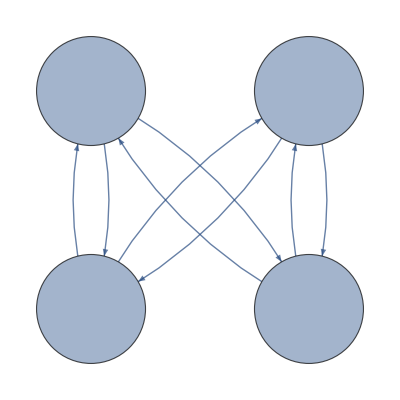

```mathematica
nodes = {"(0,0)","(0,1)","(1,0)","(1,1)"};
strat = toBin[12,4]
edges = Flatten[Table[Table[nodes[[i]]->nodes[[FromDigits[{strat[[i]],j},2]+1]],{j,0,1}],{i,1,4}]]
g = Graph[edges,VertexSize->.5,VertexLabelStyle->Directive[25],VertexLabels->Placed[Automatic,Center],VertexCoordinates->{"(0,0)"->{0,0},"(0,1)"->{1,0},"(1,0)"->{0,-1},"(1,1)"->{1,-1}}]

(*Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/stratgraph.png",g]*)
```

{(0,0)→(0,0),(0,1)→(0,0),(1,0)→(0,0),(1,1)→(1,1)}

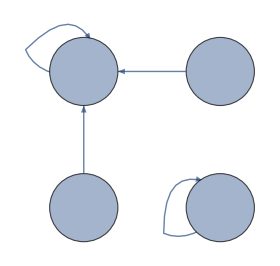

```mathematica
edges = {"(0,0)"->"(0,0)","(0,1)"->"(0,0)","(1,0)"->"(0,0)","(1,1)"->"(1,1)"}
g=Graph[edges ,VertexSize->.5,VertexLabelStyle->Directive[25],VertexLabels->Placed[Automatic,Center],VertexCoordinates->{"(0,0)"->{0,0},"(0,1)"->{1,0},"(1,0)"->{0,-1},"(1,1)"->{1,-1}}]
(*Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/stratgraphfinished.png",g]*)
```